```mathematica
lst=Table[0,8,61];
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-30,0}]~Join~Table[fCtauP[i],{i,1,30}]];
```

General::munfl: 8.59599×10^-302 8.71427×10^-17 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.32866×10^-292 (-8.53545×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.59599×10^-302 (-8.53545×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
lst
```

{{-8.0881×10^-15,-1.00691×10^-14,-1.24529×10^-14,-1.532×10^-14,-1.87668×10^-14,-2.29088×10^-14,-2.78848×10^-14,-3.3861×10^-14,-4.10367×10^-14,-4.96512×10^-14,-5.99911×10^-14,-7.24003×10^-14,-8.72912×10^-14,-1.05158×10^-13,-1.26594×10^-13,-1.52311×10^-13,-1.8316×10^-13,-2.20165×10^-13,-2.64552×10^-13,-3.17792×10^-13,-3.81648×10^-13,-4.58235×10^-13,-5.50089×10^-13,-6.60253×10^-13,-7.92375×10^-13,-9.5083×10^-13,-1.14087×10^-12,-1.36878×10^-12,-1.64213×10^-12,-1.96998×10^-12,-2.36298×10^-12,2.37896×10^-12,1.98377×10^-12,1.65421×10^-12,1.37937×10^-12,1.15018×10^-12,9.59056×10^-13,7.99676×10^-13,6.66768×10^-13,5.55936×10^-13,4.63513×10^-13,3.86442×10^-13,3.22172×10^-13,2.68578×10^-13,2.23886×10^-13,1.86617×10^-13,1.55539×10^-13,1.29624×10^-13,1.08013×10^-13,8.99912×10^-14,7.49634×10^-14,6.24318×10^-14,5.19818×10^-14,4.32677×10^-14,3.60012×10^-14,2.99417×10^-14,2.48888×10^-14,2.06753×10^-14,1.71618×10^-14,1.4232×10^-14,1.17889×10^-14},{0.0000245088,0.0000293906,0.0000352449,0.0000422652,0.0000506838,0.0000607793,0.0000728858,0.0000874036,0.000104813,0.000125691,0.000150727,0.000180749,0.000216752,0.000259926,0.0003117,0.000373786,0.000448239,0.000537523,0.00064459,0.000772984,0.000926951,0.00111159,0.001333,0.00159852,0.00191692,0.00229874,0.00275662,0.00330571,0.00396416,0.00475376,0.00571567,0.00646497,0.00682539,0.00698155,0.00702645,0.00700938,0.00695677,0.00688308,0.00679643,0.00670155,0.00660132,0.00649761,0.00639167,0.00628439,0.00617644,0.00606834,0.00596047,0.00585315,0.00574662,0.0056411,0.00553672,0.00543363,0.00533192,0.00523165,0.0051329,0.0050357,0.00494007,0.00484604,0.00475362,0.00466282,0.00457362},{0.000047257,0.00005667,0.0000679579,0.0000814941,0.0000977267,0.000117193,0.000140536,0.000168528,0.000202097,0.000242352,0.000290625,0.000348514,0.000417933,0.00050118,0.000601008,0.000720721,0.000864279,0.00103643,0.00124287,0.00149044,0.00178731,0.00214332,0.00257024,0.0030822,0.00369614,0.00443236,0.00531522,0.00637394,0.00764354,0.00916604,0.0110165,0.0123541,0.012883,0.01304,0.0130174,0.0129036,0.0127401,0.0125476,0.012337,0.0121145,0.0118843,0.0116491,0.0114109,0.0111713,0.0109316,0.0106928,0.0104557,0.0102208,0.00998883,0.00976006,0.00953483,0.00931338,0.0090959,0.00888252,0.00867332,0.00846837,0.0082677,0.0080713,0.00787918,0.0076913,0.00750763},{0.0000669012,0.000080227,0.0000962072,0.00011537,0.000138351,0.000165908,0.000198955,0.000238584,0.000286107,0.000343095,0.000411435,0.000493387,0.000591664,0.000709515,0.000850841,0.00102032,0.00122355,0.00146726,0.00175952,0.00211,0.00253028,0.00303428,0.00363867,0.00436344,0.00523258,0.00627484,0.0075247,0.00902352,0.0108209,0.0129763,0.0155878,0.0172359,0.0176584,0.0176381,0.0174383,0.0171533,0.0168203,0.0164566,0.0160722,0.015674,0.015267,0.0148552,0.0144418,0.0140295,0.0136201,0.0132155,0.012817,0.0124254,0.0120416,0.0116663,0.0112998,0.0109424,0.0105943,0.0102556,0.00992637,0.00960656,0.00929609,0.00899486,0.00870273,0.00841952,0.00814507},{0.0000827238,0.0000992013,0.000118961,0.000142656,0.000171071,0.000205147,0.000246009,0.000295011,0.000353773,0.000424239,0.000508742,0.000610077,0.000731596,0.00087732,0.00105207,0.00126163,0.00151293,0.00181428,0.00217566,0.00260903,0.00312871,0.00375191,0.00449924,0.00539542,0.00647012,0.00775888,0.00930434,0.0111576,0.0133801,0.0160452,0.0192644,0.0208974,0.0210062,0.0207247,0.020297,0.0197889,0.0192271,0.0186285,0.0180057,0.0173685,0.016725,0.0160816,0.0154434,0.0148143,0.0141975,0.0135953,0.0130094,0.0124412,0.0118915,0.0113608,0.0108494,0.0103575,0.00988478,0.00943117,0.0089963,0.00857973,0.00818101,0.00779962,0.007435,0.0070866,0.00675382},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Export["F:\\ThesisProject\\RESULTS\\16082023_corr_modified\\corr_ana_ma.dat",lst,"Table"];
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{-30,30},Joined->True]]
```

-Graphics-

{{-2.63509×10^-14,-3.23395×10^-14,-3.95375×10^-14,-4.81861×10^-14,-5.85746×10^-14,-7.10498×10^-14,-8.60277×10^-14,-1.04007×10^-13,-1.25586×10^-13,-1.51482×10^-13,-1.82556×10^-13,-2.19838×10^-13,-2.64566×10^-13,-3.18223×10^-13,-3.82589×10^-13,-4.59797×10^-13,-5.52404×10^-13,-6.6348×10^-13,-7.96702×10^-13,-9.56483×10^-13,-1.14811×10^-12,-1.37794×10^-12,-1.65357×10^-12,-1.98412×10^-12,-2.38055×10^-12,-2.85596×10^-12,-3.42612×10^-12,-4.10989×10^-12,-4.92992×10^-12,-5.9134×10^-12,-7.09297×10^-12,7.137×10^-12,5.95136×10^-12,4.96262×10^-12,4.1381×10^-12,3.45053×10^-12,2.87716×10^-12,2.39902×10^-12,2.00031×10^-12,1.66782×10^-12,1.39056×10^-12,1.15936×10^-12,9.66557×10^-13,8.05783×10^-13,6.71715×10^-13,5.59917×10^-13,4.6669×10^-13,3.8895×10^-13,3.24124×10^-13,2.70067×10^-13,2.2499×10^-13,1.87402×10^-13,1.56058×10^-13,1.29922×10^-13,1.08128×10^-13,8.99556×10^-14,7.48026×10^-14,6.21677×10^-14,5.16326×10^-14,4.28485×10^-14,3.55245×10^-14},{0.0000735264,0.0000881719,0.000105735,0.000126795,0.000152051,0.000182338,0.000218657,0.000262211,0.00031444,0.000377072,0.00045218,0.000542248,0.000650256,0.000779778,0.0009351,0.00112136,0.00134472,0.00161257,0.00193377,0.00231895,0.00278085,0.00333476,0.003999,0.00479555,0.00575076,0.00689623,0.00826987,0.00991712,0.0118925,0.0142613,0.017147,0.0193949,0.0204762,0.0209446,0.0210794,0.0210281,0.0208703,0.0206492,0.0203893,0.0201046,0.019804,0.0194928,0.019175,0.0188532,0.0185293,0.018205,0.0178814,0.0175594,0.0172399,0.0169233,0.0166102,0.0163009,0.0159958,0.015695,0.0153987,0.0151071,0.0148202,0.0145381,0.0142609,0.0139884,0.0137209},{0.000141771,0.00017001,0.000203874,0.000244482,0.00029318,0.000351578,0.000421607,0.000505585,0.000606291,0.000727056,0.000871876,0.00104554,0.0012538,0.00150354,0.00180302,0.00216216,0.00259284,0.0031093,0.00372862,0.00447132,0.00536194,0.00642997,0.00771073,0.00924661,0.0110884,0.0132971,0.0159457,0.0191218,0.0229306,0.0274981,0.0330494,0.0370624,0.0386491,0.03912,0.0390523,0.0387107,0.0382203,0.0376428,0.0370109,0.0363436,0.0356529,0.0349472,0.0342326,0.0335139,0.0327948,0.0320784,0.031367,0.0306625,0.0299665,0.0292802,0.0286045,0.0279401,0.0272877,0.0266475,0.02602,0.0254051,0.0248031,0.0242139,0.0236375,0.0230739,0.0225229},{0.000200704,0.000240681,0.000288621,0.000346111,0.000415052,0.000497724,0.000596864,0.000715752,0.00085832,0.00102929,0.00123431,0.00148016,0.00177499,0.00212854,0.00255252,0.00306095,0.00367065,0.00440179,0.00527857,0.00632999,0.00759084,0.00910283,0.010916,0.0130903,0.0156977,0.0188245,0.0225741,0.0270706,0.0324626,0.0389288,0.0467634,0.0517078,0.0529753,0.0529143,0.052315,0.05146,0.0504608,0.0493697,0.0482166,0.047022,0.045801,0.0445656,0.0433255,0.0420884,0.0408604,0.0396466,0.0384509,0.0372762,0.0361249,0.0349989,0.0338993,0.0328271,0.0317828,0.0307668,0.0297791,0.0288197,0.0278883,0.0269846,0.0261082,0.0252586,0.0244352},{0.000248171,0.000297604,0.000356882,0.000427969,0.000513214,0.00061544,0.000738027,0.000885032,0.00106132,0.00127272,0.00152623,0.00183023,0.00219479,0.00263196,0.00315621,0.00378489,0.00453878,0.00544285,0.00652699,0.00782708,0.00938613,0.0112557,0.0134977,0.0161863,0.0194104,0.0232766,0.027913,0.0334729,0.0401403,0.0481357,0.0577931,0.0626923,0.0630187,0.062174,0.0608911,0.0593666,0.0576814,0.0558856,0.054017,0.0521055,0.0501751,0.0482449,0.0463302,0.044443,0.0425925,0.0407858,0.0390282,0.0373236,0.0356744,0.0340823,0.0325483,0.0310724,0.0296543,0.0282935,0.0269889,0.0257392,0.024543,0.0233989,0.022305,0.0212598,0.0202615},{0.000283948,0.000340507,0.000408331,0.000489665,0.0005872,0.000704162,0.000844421,0.00101262,0.00121432,0.00145619,0.00174625,0.00209408,0.00251119,0.00301139,0.00361121,0.00433052,0.0051931,0.00622749,0.00746793,0.00895544,0.0107392,0.0128784,0.0154435,0.0185197,0.0222086,0.0266322,0.031937,0.0382984,0.0459269,0.055075,0.0660953,0.0700902,0.0693133,0.0676291,0.0655004,0.0630732,0.0604455,0.0576937,0.0548785,0.0520476,0.0492382,0.0464787,0.0437906,0.0411896,0.038687,0.0362903,0.0340039,0.0318301,0.0297693,0.0278204,0.0259813,0.024249,0.0226199,0.0210902,0.0196555,0.0183114,0.0170534,0.015877,0.0147777,0.0137512,0.0127932},{0.000309351,0.00037097,0.000444862,0.000533472,0.000639733,0.000767159,0.000919967,0.00110321,0.00132296,0.00158647,0.00190248,0.00228142,0.00273585,0.0032808,0.00393429,0.00471794,0.0056577,0.00678463,0.00813604,0.00975663,0.0117,0.0140305,0.0168252,0.0201765,0.0241954,0.0290148,0.0347942,0.0417247,0.0500358,0.0600022,0.0719843,0.0745765,0.0727749,0.0700649,0.0667795,0.0631275,0.0592695,0.0553284,0.0513971,0.0475443,0.0438199,0.0402583,0.0368823,0.0337055,0.0307341,0.0279694,0.0254083,0.0230448,0.0208712,0.0188779,0.0170547,0.015391,0.013876,0.0124989,0.0112491,0.0101167,0.00909202,0.0081659,0.00732981,0.00657577,0.00589636},{0.000326527,0.000391566,0.000469561,0.000563091,0.000675251,0.000809752,0.000971044,0.00116446,0.00139641,0.00167455,0.0020081,0.00240809,0.00288775,0.00346295,0.00415272,0.00497989,0.00597182,0.00716132,0.00858776,0.0102983,0.0123496,0.0148095,0.0177593,0.0212968,0.0255388,0.0306258,0.036726,0.0440413,0.0528138,0.0633336,0.0759631,0.0770432,0.074102,0.0699885,0.0651801,0.0600241,0.0547709,0.0495971,0.0446229,0.039926,0.0355527,0.031526,0.0278522,0.0245259,0.0215334,0.0188562,0.0164724,0.0143587,0.0124915,0.0108473,0.0094038,0.00813982,0.00703568,0.00607326,0.00523601,0.00450899,0.00387873,0.0033332,0.00286168,0.00245467,0.00210378}}

```mathematica
Export["F:\\ThesisProject\\RESULTS\\26052023_corr_modified\\corr_ana.dat",lst]
corr0=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_0.dat",Number];
corr1=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_1.dat",Number];
corr2=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_2.dat",Number];
corr3=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_3.dat",Number];
corr4=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_4.dat",Number];
corr5=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_5.dat",Number];
corr6=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_6.dat",Number];
corr7=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_7.dat",Number];
```

F:\ThesisProject\RESULTS\26052023_corr_modified\corr_ana.dat

```mathematica
plst=Table[0,{i,8},{j,31},{k,2}];
For[i=0,i<8,i++,plst[[i+1]]=Transpose[{Table[i,{i,-30,30}],lst[[i+1]]}]];
```

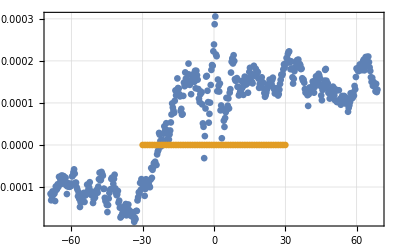

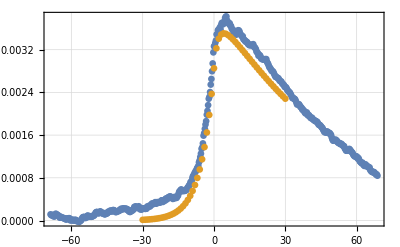

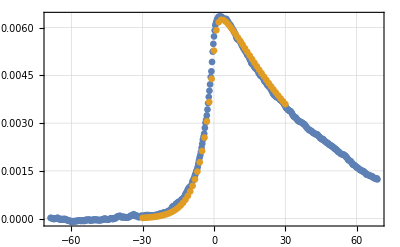

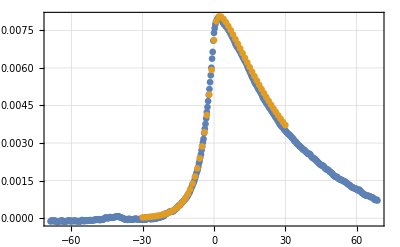

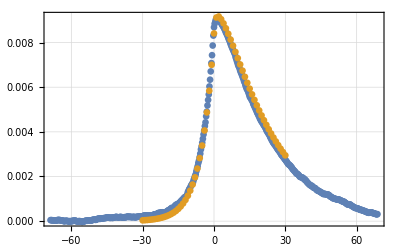

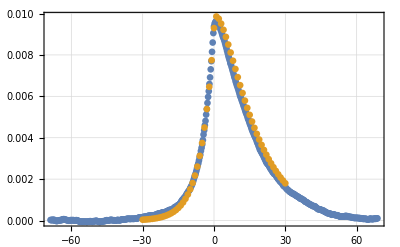

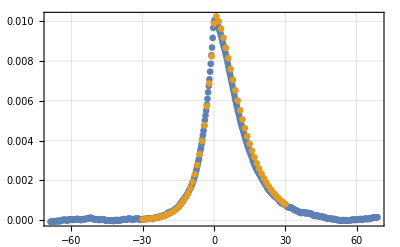

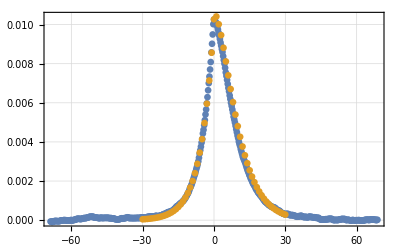

```mathematica
scalF=5.5;
pcr0=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr0}];

ListPlot[{pcr0,plst[[1]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr1=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr1}];

ListPlot[{pcr1,plst[[2]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr2=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr2}];

ListPlot[{pcr2,plst[[3]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr3=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr3}];

ListPlot[{pcr3,plst[[4]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr4=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr4}];

ListPlot[{pcr4,plst[[5]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr5=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr5}];

ListPlot[{pcr5,plst[[6]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr6=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr6}];

ListPlot[{pcr6,plst[[7]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr7=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr7}];

ListPlot[{pcr7,plst[[8]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
```

```mathematica
(**)
```

```mathematica
dlst=Table[0,8,31];
For[gg=0,gg<8,gg++,dlst[[gg+1]]=Table[lst[[gg+1,31-i]]-lst[[gg+1,31+i]],{i,-30,0}]];
```

```mathematica
Rasterize[ListPlot[dlst,PlotLegends->Table[i,{i,0,7}],DataRange->{-30,0},Joined->True]]
Export["F:\\ThesisProject\\RESULTS\\26052023_corr_modified\\DCtau_eq.dat",dlst];
```

-Graphics-

```mathematica
(*24.05.2023*)
```

```mathematica
max1=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h1.txt"],"Data"];
max4=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h4.txt"],"Data"];
max7=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h7.txt"],"Data"];
max10=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h10.txt"],"Data"];
max13=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h13.txt"],"Data"];
maxc={max1[[All,1]],max4[[All,1]],max7[[All,1]],max10[[All,1]],max13[[All,1]]};
maxc[[All,1]]=Table[0,5];
maxc//MatrixForm
maxt={max1[[All,2]],max4[[All,2]],max7[[All,2]],max10[[All,2]],max13[[All,2]]};
maxt[[All,1]]=Table[0,5];
maxt//MatrixForm
```

```mathematica
Rasterize[ListPlot[maxc,PlotLegends->Table[i,{i,1,13,3}],DataRange->{0,10},Joined->True]]
```

-Graphics-

```mathematica
Rasterize[ListPlot[maxt,PlotLegends->Table[i,{i,1,13,3}],DataRange->{0,10},PlotRange->All,Joined->True]]
```

-Graphics-

```mathematica
(*25.05.2023*)
Export["F:\\ThesisProject\\RESULTS\\25052023_extrema\\h10.dat",lst]
```

F:\ThesisProject\RESULTS\25052023_extrema\h10.dat

```mathematica
ilst=Import["F:\\ThesisProject\\RESULTS\\25052023_extrema\\h10.dat","Table"];
```

```mathematica
ilst[[1]]={0,Infinity};
```

```mathematica
fitMax=Transpose[{Table[i,{i,0,12,0.5}],ilst[[All,1]]}];
fitTMax=Transpose[{Table[i,{i,0,12,0.5}],ilst[[All,2]]}];
```

FittedModel[-0.0000219197+0.00102339 x-0.00016372 x^2+0.0000119369 x^3-3.28706×10^-7 x^4]

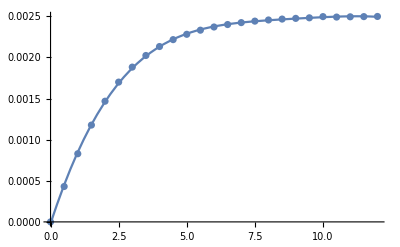

```mathematica
nlm=NonlinearModelFit[fitMax,a+b x+c x^2+d x^3+e x^4,{a,b,c,d,e},x]
Show[ListPlot[ilst[[All,1]],DataRange->{0,12},PlotRange->All],Plot[nlm[x],{x,0,12}]]
```

FittedModel[18.7195-1.50103/x-4.71804 x+0.371601 x^2-0.00456264 x^3-0.000364738 x^4]

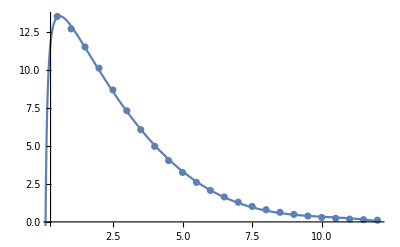

```mathematica
nlmt=NonlinearModelFit[fitTMax[[2;;25]],a+b x+c x^2+d x^3+e x^4+f x^(-1),{a,b,c,d,e,f},x]
Show[ListPlot[ilst[[All,2]],DataRange->{0,12},PlotRange->All],Plot[nlmt[x],{x,0,12}]]
```

```mathematica
Export["F:\\ThesisProject\\RESULTS\\25052023_extrema\\fit.dat",{nlm//Normal,nlmt//Normal}]
```

F:\ThesisProject\RESULTS\25052023_extrema\fit.dat

```mathematica
max1=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h1.txt"],"Data"];
max4=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h4.txt"],"Data"];
max7=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h7.txt"],"Data"];
max10=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h10.txt"],"Data"];
max13=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h13.txt"],"Data"];
maxc={max1[[All,1]],max4[[All,1]],max7[[All,1]],max10[[All,1]],max13[[All,1]]};
maxc[[All,1]]=Table[0,5];
maxc//MatrixForm
maxt={max1[[All,2]],max4[[All,2]],max7[[All,2]],max10[[All,2]],max13[[All,2]]};
maxt[[All,1]]=Table[0,5];
maxt//MatrixForm
```

(0 | 0.0562453 | 0.0887259 | 0.102058 | 0.107213 | 0.10916
0 | 0.0233935 | 0.0353066 | 0.0400117 | 0.0418152 | 0.0424933
0 | 0.00625079 | 0.0091827 | 0.0102691 | 0.0106702 | 0.0108184
0 | 0.0014678 | 0.00213307 | 0.0023707 | 0.00245623 | 0.00248632
0 | 0.000332398 | 0.000481201 | 0.000533496 | 0.000552089 | 0.000558832)

(0 | 0.269867 | 0.129315 | 0.052779 | 0.0202246 | 0.00755684
0 | 0.964786 | 0.476559 | 0.200015 | 0.0778965 | 0.0293205
0 | 3.3005 | 1.62697 | 0.679211 | 0.26338 | 0.0989795
0 | 10.101 | 4.96469 | 2.0674 | 0.800207 | 0.301444
0 | 28.5502 | 13.9992 | 5.81894 | 2.24996 | 0.843757)

{{38.3194,41.5955,43.0497,43.6496,43.9041},{15.9377,16.552,16.8776,17.0241,17.0908},{4.25861,4.30493,4.3317,4.34415,4.35119},{1.,1.,1.,1.,1.},{0.22646,0.225591,0.225038,0.224771,0.224763}}

FittedModel[-1.02185+44.2437/x]

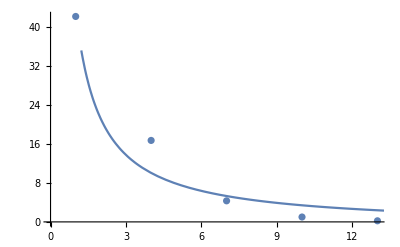

```mathematica
rate=Table[maxc[[i,2;;6]]/maxc[[4,2;;6]],{i,1,5}]
ratefit=Mean[Transpose[rate]];
ratefit=Transpose[{{1,4,7,10,13},ratefit}];
line=NonlinearModelFit[ratefit,a+b/x,{a,b,c,d},x]
Show[ListPlot[ratefit],Plot[line[x],{x,0,15}]]
```

{{0.0267168,0.0260469,0.0255292,0.0252742,0.0250688},{0.0955137,0.0959895,0.0967474,0.0973454,0.0972668},{0.326749,0.327708,0.328534,0.32914,0.328351},{1.,1.,1.,1.,1.},{2.82647,2.81974,2.81462,2.81173,2.79905}}

FittedModel[-0.0305447+0.0338354 ⅇ^(0.340939 x)]

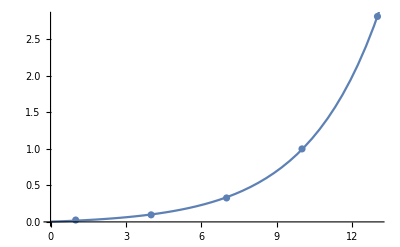

```mathematica
ratet=Table[maxt[[i,2;;6]]/maxt[[4,2;;6]],{i,1,5}]
ratetfit=Mean[Transpose[ratet]];
ratetfit=Transpose[{{1,4,7,10,13},ratetfit}];
linet=NonlinearModelFit[ratetfit,a+b Exp[c x],{a,b,c,d},x]
Show[ListPlot[ratetfit],Plot[linet[x],{x,0,15}]]
```

```mathematica
lmtM0=Limit[matJump,g->0]
eigVa0=Eigenvalues[lmtM0]
eigVeR0=Eigenvectors[lmtM0]
eigVeL0=Eigenvectors[Transpose[lmtM0]];
eigNVeL0=Table[eigVeL0[[i]]/(eigVeL0[[i]].eigVeR0[[i]]),{i,1,8}]
nessDist0=Limit[nessDist,g->0]
```

{{-3 ⅇ^(h/4),ⅇ^(-h/4),ⅇ^(-h/4),0,ⅇ^(h/4),0,0,0},{ⅇ^(h/4),-3 ⅇ^(-h/4),0,ⅇ^(-3 h/4),0,ⅇ^(-h/4),0,0},{ⅇ^(h/4),0,-3 ⅇ^(-h/4),ⅇ^(-3 h/4),0,0,ⅇ^(-h/4),0},{0,ⅇ^(-h/4),ⅇ^(-h/4),-3 ⅇ^(-3 h/4),0,0,0,ⅇ^(-3 h/4)},{ⅇ^(h/4),0,0,0,-3 ⅇ^(h/4),ⅇ^(-h/4),ⅇ^(-h/4),0},{0,ⅇ^(-h/4),0,0,ⅇ^(h/4),-3 ⅇ^(-h/4),0,ⅇ^(-3 h/4)},{0,0,ⅇ^(-h/4),0,ⅇ^(h/4),0,-3 ⅇ^(-h/4),ⅇ^(-3 h/4)},{0,0,0,ⅇ^(-3 h/4),0,ⅇ^(-h/4),ⅇ^(-h/4),-3 ⅇ^(-3 h/4)}}

{0,-4 ⅇ^(-h/4),-2 ⅇ^(-h/4),ⅇ^(-3 h/4) (-1-ⅇ^(h/2)-ⅇ^h-√(1-ⅇ^h+ⅇ^(2 h))),ⅇ^(-3 h/4) (-1-ⅇ^(h/2)-ⅇ^h+√(1-ⅇ^h+ⅇ^(2 h))),ⅇ^(-3 h/4) Root[48 ⅇ^(3 h/2)+(14 ⅇ^(h/2)+16 ⅇ^h+14 ⅇ^(3 h/2)) #1+(4+4 ⅇ^(h/2)+4 ⅇ^h) #1^2+#1^3&,1],ⅇ^(-3 h/4) Root[48 ⅇ^(3 h/2)+(14 ⅇ^(h/2)+16 ⅇ^h+14 ⅇ^(3 h/2)) #1+(4+4 ⅇ^(h/2)+4 ⅇ^h) #1^2+#1^3&,2],ⅇ^(-3 h/4) Root[48 ⅇ^(3 h/2)+(14 ⅇ^(h/2)+16 ⅇ^h+14 ⅇ^(3 h/2)) #1+(4+4 ⅇ^(h/2)+4 ⅇ^h) #1^2+#1^3&,3]}

{{ⅇ^-h,ⅇ^(-h/2),ⅇ^(-h/2),1,ⅇ^-h,ⅇ^(-h/2),ⅇ^(-h/2),1},6,{(ⅇ^(-3 h/2) (48 ⅇ^(2 h)+28 ⅇ^h Root[48 ⅇ^111+1+1+#1^3&,3]+12+3 ⅇ^h 1^4+Root[48 ⅇ^1+1+1+#1^3&,3]^5))/(2 (24 ⅇ^(3 h/2)+6 ⅇ^(h/2) Root[48 ⅇ^1+(1) #1+(1) 1+#1^3&,3]+3+ⅇ^1 1^2+ⅇ^h Root[48 ⅇ^1+1+1+#1^3&,3]^2)),1/(2 1),4,1,1}}
 |  |  |  |

{{1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2))},6,{(ⅇ^(-h/2) (48 ⅇ^(2 h)+28 ⅇ^h Root[1]+92 ⅇ^1 Root[1&,3]+10+1+3 ⅇ^h 1^4+Root[1&,3]^5))/(2 1 (1+(1)^2/(1)^2+1/1+1+(ⅇ^1 1)/(2 1^2)+(ⅇ^(-2 h) (1)^2)/(4 (1)^2))),6,1/1}}
 |  |  |  |

{1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2),1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2)}

```mathematica
Limit[nessDist,g->Infinity]
```

{1/((1+ⅇ^(h/2))^2),ⅇ^(h/2)/((1+ⅇ^(h/2))^2),ⅇ^(h/2)/((1+ⅇ^(h/2))^2),0,0,0,0,ⅇ^h/((1+ⅇ^(h/2))^2)}

{1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2),1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2)}

```mathematica
xExp0=Dot[nessDist0,xL];
yExp0=Dot[nessDist0,yL];
{seigenVa,seigenVeL,nseigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigVa0,eigVeL0,eigNVeL0,eigVeR0,nessDist0,xExp0,yExp0};
```

```mathematica
lst[[3]]=Table[fCtauN[i]/.h->7,{i,-30,0}]~Join~Table[fCtauP[i]/.h->7,{i,1,30}];
```

General::munfl: 8.59599×10^-302 (-2.71051×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.32866×10^-292 (-2.71051×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Rasterize[ListPlot[{lst[[3]],lst[[1]],lst[[2]]},DataRange->{-30,30},PlotRange->All,Joined->True,AxesLabel->{"τ","C(τ)"},PlotLegends->Placed[{"γ→0","γ=10","γ→∞"},{0.8,0.8}]]]
```

-Graphics-

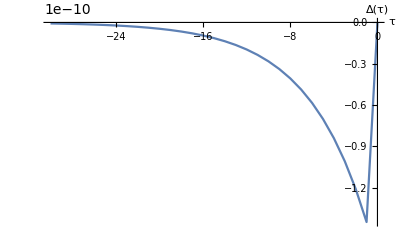

```mathematica
ListPlot[Table[lst[[31+i]]-lst[[31-i]],{i,30,0,-1}],DataRange->{-30,0},Joined->True,AxesLabel->{"τ","Δ(τ)"}]
```

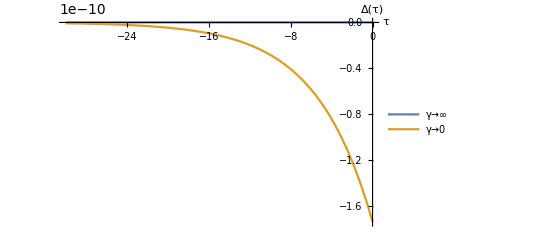

```mathematica
Plot[{fIDCtau[t]/.h->7,fDCtau[t]/.h->7},{t,-30,0},PlotRange->All,AxesLabel->{"τ","Δ(τ)"},PlotLegends->Placed[{"γ→∞","γ→0"},{0.1,0.8}]]
```

```mathematica
(*EQ degeneration*)
x1=1;
x2=1;
yLst={0,0,0,0,1,1,1,1};
mLst={0,1,0,1,0,1,0,1};
aLst={0,0,1,1,0,0,1,1};
fH[hh_,ii_]:=Exp[-hh*((x1-1/2)*(mLst[[ii]]-1/2)+(x2-1/2)*(aLst[[ii]]))];
matJump=Transpose[({{-(fH[h,1]*3), fH[h,1], fH[h,1], 0, fH[h,1], 0, 0, 0}, {fH[h,2], -(fH[h,2]*3), 0, fH[h,2], 0, fH[h,2], 0, 0}, {fH[h,3], 0, -(fH[h,3]*3), fH[h,3], 0, 0, fH[h,3], 0}, {0, fH[h,4], fH[h,4], -(fH[h,4]*3), 0, 0, 0, fH[h,4]}, {fH[h,5], 0, 0, 0, -(fH[h,5]*3), fH[h,5], fH[h,5], 0}, {0, fH[h,6], 0, 0, fH[h,6], -(fH[h,6]*3), 0, fH[h,6]}, {0, 0, fH[h,7], 0, fH[h,7], 0, -(fH[h,7]*3), fH[h,7]}, {0, 0, 0, fH[h,8], 0, fH[h,8], fH[h,8], -(fH[h,8])}})];
eigenVa=Eigenvalues[matJump];
eigenVeR=Eigenvectors[matJump];
eigenVeL=Eigenvectors[Transpose[matJump]];
```

```mathematica
xL={1,2,3,4,1,2,3,4};
yL={1,1,1,1,2,2,2,2};
matA=-TensorProduct[yL,xL]+TensorProduct[xL,yL];
matPA=TensorProduct[xL,yL];
matNA=TensorProduct[yL,xL];
(* Find NESS distributions*)
fWTilde[ww_]:=Join[ww[[1;;Dimensions[ww][[1]]-1]],{Table[1,Dimensions[ww][[2]]]}];
nessDist=Dot[Inverse[fWTilde[matJump]],Transpose[Table[0,Dimensions[fWTilde[matJump]][[2]]-1]~Join~{1}]];
xExp=xL.nessDist;
yExp=yL.nessDist;
fDCtau[t_]:=N[(Sum[Exp[-seigenVa[[i]]*t]*Tr[Dot[TensorProduct[seigenVeR[[i]],nseigenVeL[[i]]*snessDist],matA]],{i,8}])/(sxExp*syExp)];
fCtauP[t_]:=
N[(Sum[Exp[seigenVa[[i]]*t]*Tr[Dot[TensorProduct[seigenVeR[[i]],nseigenVeL[[i]]*snessDist],matPA]],{i,8}])/(sxExp*syExp)-1];
fCtauN[t_]:=N[(Sum[Exp[-seigenVa[[i]]*t]*Tr[Dot[TensorProduct[seigenVeR[[i]],nseigenVeL[[i]]*snessDist],matNA]],{i,8}])/(sxExp*syExp)-1];
```

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.h->7;
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];
Rasterize[Plot[fDCtau[t],{t,-30,0},AxesLabel->{"τ","Δ(τ)"}]]
```

-Graphics-

```mathematica
lst=Table[fDCtau[i],{i,-30,0,0.5}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*Compare ana and sim*)
lst=Table[N[nessDist/.{h->7,g->i}],{i,0,20}];
```

```mathematica
Export["F:\\ThesisProject\\RESULTS\\01062023_testanasim\\ana_h20.dat",lst]
```

F:\ThesisProject\RESULTS\01062023_testanasim\ana_h20.dat

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->13,h->13};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];maxima=Maximize[fCtauP[t],{t}∈Interval[{0.1,0.4}]];lst[[5,13]]={maxima[[1]],maxima[[2,1,2]]}
```

General::munfl: 1.3816×10^-193 (-5.49043×10^-206) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-0.00375097,0.4}

```mathematica
lstRatio=Table[lst[[i,j,1]]/lst[[i,j,2]],{i,5},{j,15}]
```

{{0.0867457,0.208418,0.393473,0.686122,1.15948,1.93368,3.20602,5.30114,8.75374,14.4451,23.828,39.2973,64.8017,106.856,176.14},{0.0106245,0.0242473,0.043896,0.0740866,0.122143,0.200043,0.327465,0.536805,0.881428,1.44927,2.38525,3.92826,6.47238,10.6639,17.5397},{0.000847066,0.00189389,0.00337684,0.00564405,0.00925494,0.0151192,0.0247248,0.0405127,0.0664982,0.1093,0.17983,0.296084,0.487779,0.803082,1.3256},{0.0000653776,0.000145312,0.000257906,0.000429647,0.000702941,0.00114671,0.00187373,0.0030695,0.00503892,0.00824791,0.013635,0.0224413,0.036977,0.0608623,0.10021},{5.24198×10^-6,0.0000116426,0.0000206624,0.0000343736,0.0000562117,0.0000916827,0.00014979,0.000245369,0.000402761,0.000662315,0.00108912,0.0017932,-0.00937742,0.0051461,0.00774487}}

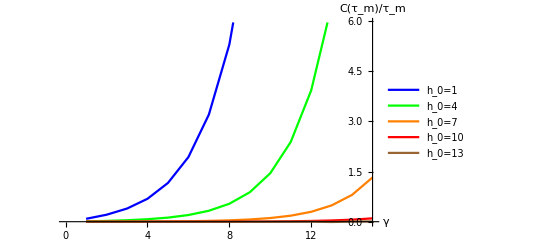

F:\ThesisProject\RESULTS\01062023_testanasim\ratio.png

```mathematica
ListLinePlot[lstRatio,AxesLabel->{"γ","C(τ_m)/τ_m"},PlotLegends->{"h_0=1","h_0=4","h_0=7","h_0=10","h_0=13"},PlotStyle->{Blue,Green,Orange,Red,Brown},AxesOrigin->{15,0}]
Export["F:\\ThesisProject\\RESULTS\\01062023_testanasim\\ratio.png",%]
```

```mathematica
Rasterize[ListLinePlot[{lstRatio[[4,All]],lstRatio[[5,All]]},PlotStyle->{Red,Brown}]]
Export["F:\\ThesisProject\\RESULTS\\01062023_testanasim\\ratio_inset.png",%]
```

-Graphics-

F:\ThesisProject\RESULTS\01062023_testanasim\ratio_inset.png

```mathematica
(*Examine eigenvalue*)

lst=Table[0,4,61];
For[gg=0,gg<4,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->7,h->(2*gg+5)};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-30,0}]~Join~Table[fCtauP[i],{i,1,30}]];
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{-30,30},PlotRange->All,Joined->True]]
```

General::munfl: Exp[-3680.64] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3557.96] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3435.27] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
Rasterize[ListPlot[lst[[2;;4,All]],PlotLegends->Table[i,{i,0,7}],DataRange->{-30,30},PlotRange->All,Joined->True]]
Export["F:\\ThesisProject\\RESULTS\\07062023_ana\\corr_hlines_2ip5.dat",lst]
```

-Graphics-

F:\ThesisProject\RESULTS\07062023_ana\corr_hlines_2ip5.dat

```mathematica
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];Print[N[seigenVa]];
Print[N[nseigenVeL]]]
```

```mathematica
(*08.06.2023 Expansion*)
Eigensystem[{{0,a,a,0},{1/a,0,0,a},{1/a,0,0,a},{0,1/a,1/a,0}}]
```

{{0,0,-2,2},{{-a^2,0,0,1},{0,-1,1,0},{a^2,-a,-a,1},{a^2,a,a,1}}}

```mathematica
Eigensystem[Transpose[{{0,a,a,0},{1/a,0,0,a},{1/a,0,0,a},{0,1/a,1/a,0}}]]
```

{{0,0,-2,2},{{-1/a^2,0,0,1},{0,-1,1,0},{1/a^2,-1/a,-1/a,1},{1/a^2,1/a,1/a,1}}}

```mathematica
eigenVa
```

{0,-2 ⅇ^(-h/2) (1+ⅇ^h),-ⅇ^(-h/2) (1+ⅇ^h),-ⅇ^(-h/2) (1+ⅇ^h),-ⅇ^(-h/2) (1+ⅇ^h),ⅇ^(-2-g-h/2) Root[2 ⅇ^(6+3 g+2 h)-2 ⅇ^(4+4 g+2 h)+(2 ⅇ^(4+2 g)+5 ⅇ^(4+2 g+h)-ⅇ^(2+3 g+h)+2 ⅇ^(4+2 g+2 h)) #1+(3 ⅇ^(2+g)+3 ⅇ^(2+g+h)) #1^2+#1^3&,1],ⅇ^(-2-g-h/2) Root[2 ⅇ^(6+3 g+2 h)-2 ⅇ^(4+4 g+2 h)+(2 ⅇ^(4+2 g)+5 ⅇ^(4+2 g+h)-ⅇ^(2+3 g+h)+2 ⅇ^(4+2 g+2 h)) #1+(3 ⅇ^(2+g)+3 ⅇ^(2+g+h)) #1^2+#1^3&,2],ⅇ^(-2-g-h/2) Root[2 ⅇ^(6+3 g+2 h)-2 ⅇ^(4+4 g+2 h)+(2 ⅇ^(4+2 g)+5 ⅇ^(4+2 g+h)-ⅇ^(2+3 g+h)+2 ⅇ^(4+2 g+2 h)) #1+(3 ⅇ^(2+g)+3 ⅇ^(2+g+h)) #1^2+#1^3&,3]}

```mathematica
nessDist//MatrixForm
```

LinearSolveFunction[…]

```mathematica
MatrixRank[matJump]
```

6

```mathematica
nessDist
```

{ⅇ^g/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^(g+h)/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^(g+h)/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^(2 h)/((1+ⅇ^g) (1+ⅇ^h)^2),1/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^h/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^h/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^(g+2 h)/((1+ⅇ^g) (1+ⅇ^h)^2)}

```mathematica
lst=Table[0,8,201];
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-10,0,0.1}]~Join~Table[fCtauP[i],{i,1,10,0.1}]];
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{-10,10},PlotRange->All,Joined->True]]
```

-Graphics-

```mathematica
Export["F:\\ThesisProject\\RESULTS\\08062023_expasion\\corr_zeroorder.png",%]
```

F:\ThesisProject\RESULTS\08062023_expasion\corr_zeroorder.png

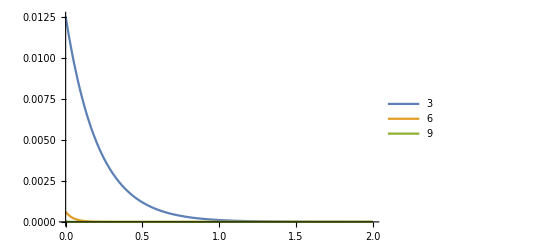

```mathematica
f0corr[g_,h_,t_]:=(E^(2 h-E^(-h/2) (1+E^h) t) (-1+E^g) (1+3 E^h+2 E^(2 h)))/((1+4 E^h) (1+E^(2 h)) (2+E^g+4 E^h+E^(2 h)+2 E^(g+h)+2 E^(g+2 h)));
Plot[{f0corr[7,3,t],f0corr[7,6,t],f0corr[7,9,t]},{t,0,2},PlotLegends->{3,6,9},PlotRange->All]
```

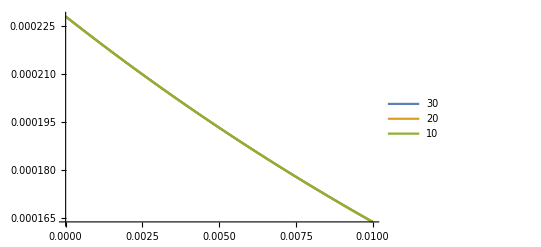

```mathematica
Plot[{fCtauP[t]/.{g->30,h->7},fCtauP[t]/.{g->20,h->7},fCtauP[t]/.{g->10,h->7}},{t,0,0.01},PlotRange->All,PlotLegends->{30,20,10}]
```

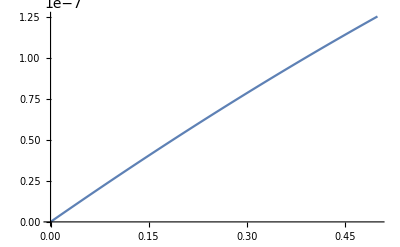

```mathematica
Plot[(Exp[x]-1)/(2*Exp[x+7]+2*Exp[x+14]+Exp[x]+4*Exp[7]+Exp[14]+2),{x,0,0.5}]
```

```mathematica
(*09.06.2023 Closer to corr*)
lst=Table[0,5,31];
For[gg=1,gg<=5,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg*2,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg]]=Table[fCtauP[i],{i,0,6,0.2}]];
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,2,10,2}],DataRange->{0,6},PlotRange->All,Joined->True]]
```

General::munfl: Exp[-713.419] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-738.898] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-764.377] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
lstn=Table[0,15];
lstp=Table[0,15];
lstd=Table[0,15];
For[gg=1,gg<=15,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lstn[[gg]]=fCtauN[0];lstp[[gg]]=fCtauP[0];];
lstd=lstp-lstn
lstn
lstp
```

General::munfl: 9.16972×10^-152 (-4.11653×10^-160) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{6.93223×10^-13,8.96372×10^-12,2.02935×10^-11,1.33589×10^-11,-4.69624×10^-13,-2.18185×10^-11,1.44781×10^-8,-6.09801×10^-12,3.05054×10^-11,2.01195×10^-12,-1.53296×10^-10,-3.05682×10^-10,4.67217×10^-9,-2.94254×10^-8,1.32346×10^-8}

{0.00285236,0.00527807,0.0071108,0.00840853,0.00929614,0.00988645,0.0102691,0.010512,0.0106638,0.0107576,0.0108151,0.0108503,0.0108717,0.0108848,0.0108927}

{0.00285236,0.00527807,0.0071108,0.00840853,0.00929614,0.00988645,0.0102691,0.010512,0.0106638,0.0107576,0.0108151,0.0108503,0.0108717,0.0108847,0.0108927}

```mathematica
Export["F:\\ThesisProject\\RESULTS\\09062023_testonfeed\\diff_t0.dat",{lstd,lstp,lstn}]
```

F:\ThesisProject\RESULTS\09062023_testonfeed\diff_t0.dat

```mathematica
Rasterize[Plot[{conditionP[t,1,1],conditionP[t,1,2],conditionP[t,1,3],conditionP[t,1,4],conditionP[t,1,5],conditionP[t,1,6],conditionP[t,1,7],conditionP[t,1,8]},{t,0,10},PlotLegends->Placed[{"From (0,0,0)","From (1,0,0)","From (0,1,0)","From (1,1,0)", "From (0,0,1)","From (1,0,1)","From (0,1,1)","From (1,1,1)"},{0.8,0.4}],LabelStyle->7,AxesLabel->{"time","P(0,0,0)"},PlotRange->{-0.1,1.1}]]
Export["F:\\ThesisProject\\RESULTS\\22062023_complementary\\transient_eq_tos1.png",%]
```

-Graphics-

F:\ThesisProject\RESULTS\22062023_complementary\transient_eq_tos1.png

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->15,h->6};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];
Rasterize[Plot[{conditionP[t,8,1],conditionP[t,8,2],conditionP[t,8,3],conditionP[t,8,4],conditionP[t,8,5],conditionP[t,8,6],conditionP[t,8,7],conditionP[t,8,8]},{t,0,20},PlotLegends->Placed[{"From (0,0,0)","From (1,0,0)","From (0,1,0)","From (1,1,0)", "From (0,0,1)","From (1,0,1)","From (0,1,1)","From (1,1,1)"},{0.8,0.4}],LabelStyle->7,AxesLabel->{"time","P(1,1,1)"},PlotRange->{-0.1,1.1}]]
Export["F:\\ThesisProject\\RESULTS\\22062023_complementary\\transient_neq_tos8.png",%]
```

General::munfl: -7.25934×10^-151 (-2.69281×10^-158) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

F:\ThesisProject\RESULTS\22062023_complementary\transient_neq_tos8.png

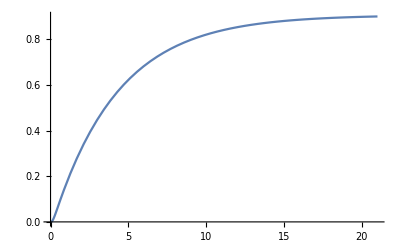

```mathematica
(*17.08.2023 Process correlation*)
Plot[tProp[8,1,t,0],{t,0,21}]
```

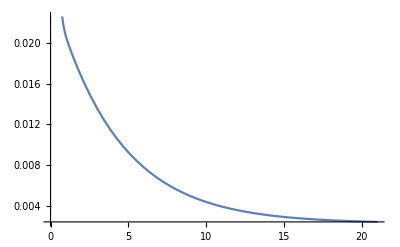

```mathematica
Plot[tProp[1,1,t,0],{t,0,21}]
```

```mathematica
eigenVeR[[2]]
```

{-8.55017×10^-15,0.5,-0.5,1.71774×10^-13,8.55213×10^-15,-0.5,0.5,-1.71856×10^-13}

```mathematica
eigenVeR[[0]]
```

List

```mathematica
eigenVeR[[2,2]]
```

0.5

```mathematica
propres=Table[Sum[Exp[eigenVa[[i]]*35]*eigenVeR[[i,j]]*eigenVeL[[i,1]],{i,1,8}],{j,1,8}]
```

General::munfl: Exp[-283922.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14135.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.00225448,0.0452546,0.0452546,0.00100466,2.06085×10^-9,0.0000249393,0.0000249393,0.906182}

```mathematica
eigenVeR[[8]]/propres
```

{1.09797,1.09804,1.09804,1.09801,1.09985,1.1008,1.1008,1.1008}

General::munfl: Exp[-283922.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14135.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

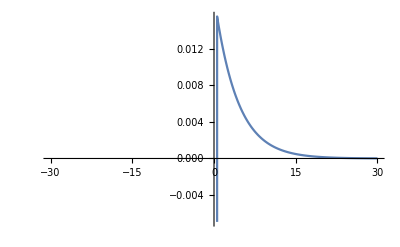

```mathematica
Plot[fCtauP[tau,35,initstate],{tau,-30,30}]
```

General::munfl: Exp[-283922.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14135.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

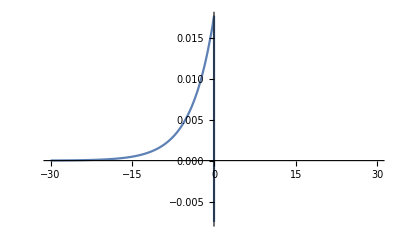

```mathematica
Plot[fCtauN[tau,35,initstate],{tau,-30,30}]
```

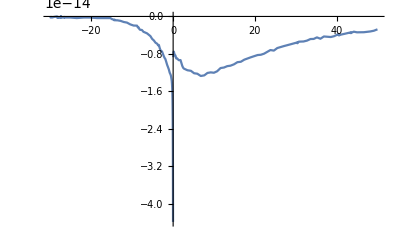
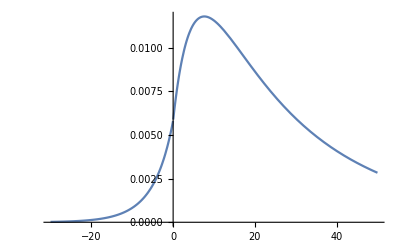
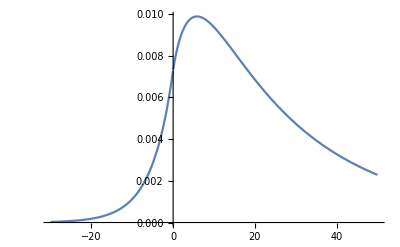
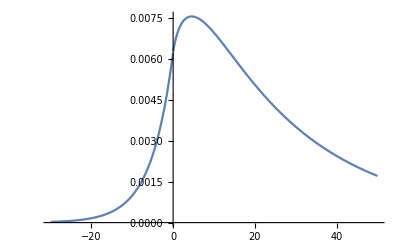
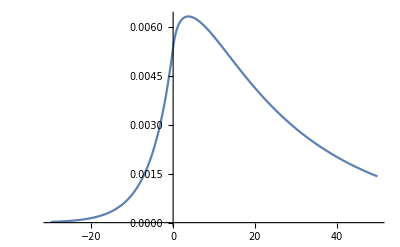
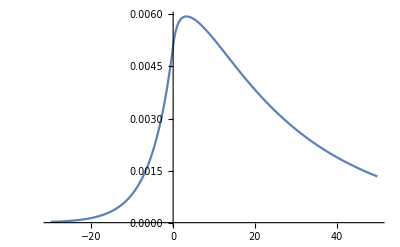
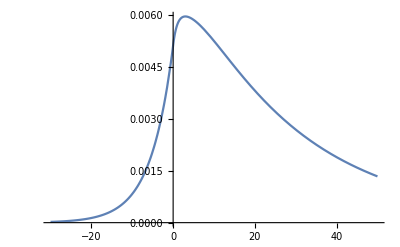
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}[3]

```mathematica
corrtimelst[3]
```

```mathematica
Table[fCtau[tau,t,initstate],{t,0,30,5}]
```

General::munfl: Exp[-772.739] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{Piecewise[{{1, tau<0}, {-2.39808×10^-14 (1.1986×10^-6 ⅇ^(-38.6369 tau)+6.43406×10^-7 ⅇ^(-11.6856 tau)-1.58717×10^-34 ⅇ^(-1.16512 tau)-0.0000419575 ⅇ^(-1.11344 tau)-3.08048×10^-33 ⅇ^(-0.347548 tau)-0.0000418355 ⅇ^(-0.181643 tau)+0.0000145522 ⅇ^(-0.0334946 tau)+0.0000673988 ⅇ^(1.4366×10^-16 tau))+96, tau≥0}, {0, True}}],Piecewise[{{0.000635947 (0.000791808 ⅇ^(-1.4366×10^-16 tau)+0.0000318128 ⅇ^(0.0334946 tau)+0.0137679 ⅇ^(0.181643 tau)+1.40694×10^-32 ⅇ^(0.347548 tau)-0.0013527 ⅇ^(1.11344 tau)+6.7036×10^-34 ⅇ^(1.16512 tau)+0.93798 ⅇ^(11.6856 tau)-0.951219 ⅇ^(38.6369 tau))+65, tau<0}, {0.459986 (1.1986×10^-6 ⅇ^(-38.6369 tau)+10+0.0000673988 ⅇ^(1.4366×10^-16 tau))+65, tau≥0}, {0, True}}],Piecewise[{{0.000311699 (0.000791808 ⅇ^(-1.4366×10^-16 tau)+0.0000318128 ⅇ^(0.0334946 tau)+0.0137679 ⅇ^(0.181643 tau)+1.40694×10^-32 ⅇ^(0.347548 tau)-0.0013527 ⅇ^(1.11344 tau)+6.7036×10^-34 ⅇ^(1.16512 tau)+0.93798 ⅇ^(11.6856 tau)-0.951219 ⅇ^(38.6369 tau))+65, tau<0}, {1.0775 (1.1986×10^-6 ⅇ^(-38.6369 tau)+9+1+0.0000673988 ⅇ^(1.4366×10^-16 3))+65, tau≥0}, {0, True}}],Piecewise[{{0.000184658 (0.000791808 ⅇ^(-1.4366×10^-16 tau)+0.0000318128 ⅇ^(0.0334946 tau)+0.0137679 ⅇ^(0.181643 tau)+1.40694×10^-32 ⅇ^(0.347548 tau)-0.0013527 ⅇ^(1.11344 tau)+6.7036×10^-34 ⅇ^(1.16512 tau)+0.93798 ⅇ^(11.6856 tau)-0.951219 ⅇ^(38.6369 tau))+0.000553974 (1)+64, tau<0}, {1.68396 (1.1986×10^-6 ⅇ^(-38.6369 tau)+10+0.0000673988 ⅇ^1)+65, tau≥0}, {0, True}}],Piecewise[{{0.00013674 (0.000791808 ⅇ^(-1.4366×10^-16 tau)+0.0000318128 ⅇ^(0.0334946 tau)+0.0137679 ⅇ^(0.181643 tau)+1.40694×10^-32 ⅇ^(0.347548 tau)-0.0013527 ⅇ^(1.11344 tau)+6.7036×10^-34 ⅇ^(1.16512 tau)+0.93798 ⅇ^(11.6856 tau)-0.951219 ⅇ^(38.6369 tau))+65, tau<0}, {2.23081 (1.1986×10^-6 ⅇ^(-38.6369 tau)+9+24 1+0.0000673988 ⅇ^(24 tau))+65, tau≥0}, {0, True}}],Piecewise[{{0.000120219 (0.000791808 ⅇ^(-1.4366×10^-16 tau)+0.0000318128 ⅇ^(0.0334946 tau)+0.0137679 ⅇ^(0.181643 tau)+1.40694×10^-32 ⅇ^(0.347548 tau)-0.0013527 ⅇ^(1.11344 tau)+6.7036×10^-34 ⅇ^(1.16512 tau)+0.93798 ⅇ^(11.6856 tau)-0.951219 ⅇ^(38.6369 tau))+65, tau<0}, {2.70702 (1.1986×10^-6 ⅇ^(-38.6369 tau)+10+0.0000673988 ⅇ^(1.4366×10^-16 tau))+65, tau≥0}, {0, True}}],{ | 1}
 |  |  |  |

```mathematica
Plot[{fCtau[tau,0,initstate],fCtau[tau,5,initstate],fCtau[tau,10,initstate],fCtau[tau,15,initstate],fCtau[tau,20,initstate],fCtau[tau,25,initstate],fCtau[tau,30,initstate]},{tau,-30,50},PlotLegends->Table[t,{t,0,30,5}]]
```

```mathematica
samplingpoints=Table[Table[fCtau[tau,t,initstate],{tau,-50,50,0.25}],{t,0,25,5}]
```

General::munfl: Exp[-1931.85] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-8.88178×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-8.88178×10^-16,-8.88178×10^-16,-4.44089×10^-16,-8.88178×10^-16,-8.88178×10^-16,-4.44089×10^-16,-8.88178×10^-16,-8.88178×10^-16,-8.88178×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,0.,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-8.88178×10^-16,-8.88178×10^-16,-8.88178×10^-16,-8.88178×10^-16,-4.44089×10^-16,-4.44089×10^-16,-8.88178×10^-16,-8.88178×10^-16,-8.88178×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-8.88178×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-8.88178×10^-16,-4.44089×10^-16,-8.88178×10^-16,-4.44089×10^-16,-8.88178×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-8.88178×10^-16,-4.44089×10^-16,-4.44089×10^-16,-8.88178×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,-8.88178×10^-16,-8.88178×10^-16,-8.88178×10^-16,-4.44089×10^-16,-4.44089×10^-16,-8.88178×10^-16,-8.88178×10^-16,-8.88178×10^-16,-4.44089×10^-16,-8.88178×10^-16,-8.88178×10^-16,-4.44089×10^-16,-1.33227×10^-15,-1.33227×10^-15,-8.88178×10^-16,-8.88178×10^-16,-1.33227×10^-15,-1.33227×10^-15,-1.33227×10^-15,-8.88178×10^-16,-8.88178×10^-16,-8.88178×10^-16,-8.88178×10^-16,-8.88178×10^-16,-8.88178×10^-16,-8.88178×10^-16,0.,-8.88178×10^-16,-8.88178×10^-16,-1.33227×10^-15,-1.33227×10^-15,-1.33227×10^-15,-1.33227×10^-15,-1.33227×10^-15,-1.33227×10^-15,-8.88178×10^-16,-8.88178×10^-16,-1.33227×10^-15,-1.33227×10^-15,-2.22045×10^-15,-2.22045×10^-15,-2.22045×10^-15,-1.77636×10^-15,-8.88178×10^-16,-1.33227×10^-15,-2.22045×10^-15,-2.22045×10^-15,-1.77636×10^-15,-1.77636×10^-15,-2.22045×10^-15,-3.10862×10^-15,-2.66454×10^-15,-2.66454×10^-15,-2.66454×10^-15,-2.66454×10^-15,-2.66454×10^-15,-3.10862×10^-15,-3.10862×10^-15,-3.9968×10^-15,-3.55271×10^-15,-3.9968×10^-15,-4.44089×10^-15,-4.44089×10^-15,-3.55271×10^-15,-3.9968×10^-15,-4.44089×10^-15,-5.32907×10^-15,-4.88498×10^-15,-5.77316×10^-15,-6.66134×10^-15,-6.66134×10^-15,-6.66134×10^-15,-7.54952×10^-15,-6.66134×10^-15,-6.66134×10^-15,-7.10543×10^-15,-7.99361×10^-15,-8.43769×10^-15,-1.02141×10^-14,-1.02141×10^-14,-1.02141×10^-14,-1.06581×10^-14,-1.11022×10^-14,-1.15463×10^-14,-1.19904×10^-14,-1.24345×10^-14,-1.24345×10^-14,-1.37668×10^-14,-1.42109×10^-14,-1.42109×10^-14,-1.5099×10^-14,-1.59872×10^-14,-1.68754×10^-14,-1.68754×10^-14,-1.73195×10^-14,-1.82077×10^-14,-1.95399×10^-14,-1.9984×10^-14,-2.08722×10^-14,-2.26485×10^-14,-2.30926×10^-14,-2.39808×10^-14,-2.53131×10^-14,-2.57572×10^-14,-2.70894×10^-14,-2.84217×10^-14,-2.93099×10^-14,-3.01981×10^-14,-3.19744×10^-14,-3.28626×10^-14,-3.64153×10^-14,-1.06581×10^-14,-7.99361×10^-15,-8.43769×10^-15,-9.10383×10^-15,-9.32587×10^-15,-9.99201×10^-15,-9.99201×10^-15,-9.99201×10^-15,-1.02141×10^-14,-1.11022×10^-14,-1.13243×10^-14,-1.17684×10^-14,-1.17684×10^-14,-1.19904×10^-14,-1.19904×10^-14,-1.22125×10^-14,-1.22125×10^-14,-1.24345×10^-14,-1.26565×10^-14,-1.28786×10^-14,-1.33227×10^-14,-1.31006×10^-14,-1.33227×10^-14,-1.35447×10^-14,-1.33227×10^-14,-1.33227×10^-14,-1.35447×10^-14,-1.33227×10^-14,-1.35447×10^-14,-1.37668×10^-14,-1.39888×10^-14,-1.37668×10^-14,-1.37668×10^-14,-1.37668×10^-14,-1.37668×10^-14,-1.35447×10^-14,-1.37668×10^-14,-1.39888×10^-14,-1.37668×10^-14,-1.35447×10^-14,-1.37668×10^-14,-1.39888×10^-14,-1.35447×10^-14,-1.35447×10^-14,-1.33227×10^-14,-1.33227×10^-14,-1.26565×10^-14,-1.28786×10^-14,-1.28786×10^-14,-1.26565×10^-14,-1.31006×10^-14,-1.31006×10^-14,-1.24345×10^-14,-1.26565×10^-14,-1.26565×10^-14,-1.24345×10^-14,-1.26565×10^-14,-1.26565×10^-14,-1.24345×10^-14,-1.22125×10^-14,-1.24345×10^-14,-1.24345×10^-14,-1.19904×10^-14,-1.19904×10^-14,-1.19904×10^-14,-1.17684×10^-14,-1.17684×10^-14,-1.19904×10^-14,-1.19904×10^-14,-1.15463×10^-14,-1.15463×10^-14,-1.17684×10^-14,-1.17684×10^-14,-1.13243×10^-14,-1.13243×10^-14,-1.11022×10^-14,-1.08802×10^-14,-1.11022×10^-14,-1.06581×10^-14,-1.08802×10^-14,-1.06581×10^-14,-1.08802×10^-14,-1.08802×10^-14,-1.06581×10^-14,-1.06581×10^-14,-1.06581×10^-14,-1.04361×10^-14,-1.04361×10^-14,-1.04361×10^-14,-1.04361×10^-14,-1.04361×10^-14,-9.76996×10^-15,-9.76996×10^-15,-9.76996×10^-15,-9.76996×10^-15,-9.76996×10^-15,-9.76996×10^-15,-9.54792×10^-15,-9.54792×10^-15,-9.76996×10^-15,-9.32587×10^-15,-9.32587×10^-15,-9.10383×10^-15,-9.10383×10^-15,-9.10383×10^-15,-8.88178×10^-15,-9.10383×10^-15,-9.10383×10^-15,-9.10383×10^-15,-8.88178×10^-15,-8.65974×10^-15,-8.88178×10^-15,-8.65974×10^-15,-7.99361×10^-15,-8.21565×10^-15,-8.21565×10^-15,-8.43769×10^-15,-8.43769×10^-15,-7.99361×10^-15,-7.77156×10^-15,-7.77156×10^-15,-7.99361×10^-15,-7.54952×10^-15,-7.54952×10^-15,-7.54952×10^-15,-7.77156×10^-15,-7.54952×10^-15,-7.54952×10^-15,-7.77156×10^-15,-7.10543×10^-15,-7.54952×10^-15,-7.32747×10^-15,-7.54952×10^-15,-7.32747×10^-15,-6.88338×10^-15,-7.10543×10^-15,-6.88338×10^-15,-7.10543×10^-15,-6.88338×10^-15,-6.66134×10^-15,-6.66134×10^-15,-6.88338×10^-15,-6.43929×10^-15,-6.88338×10^-15,-6.88338×10^-15,-6.66134×10^-15,-6.43929×10^-15,-6.21725×10^-15,-6.43929×10^-15,-5.9952×10^-15,-6.21725×10^-15,-6.43929×10^-15,-5.9952×10^-15,-6.43929×10^-15,-6.43929×10^-15,-6.43929×10^-15,-6.43929×10^-15,-6.21725×10^-15,-5.9952×10^-15,-5.9952×10^-15,-5.9952×10^-15,-5.32907×10^-15,-5.77316×10^-15,-5.32907×10^-15,-5.55112×10^-15,-5.32907×10^-15,-5.32907×10^-15,-5.77316×10^-15,-5.32907×10^-15,-5.55112×10^-15,-5.32907×10^-15,-5.32907×10^-15,-5.32907×10^-15,-5.32907×10^-15,-5.32907×10^-15,-4.88498×10^-15,-5.10703×10^-15,-4.88498×10^-15,-5.10703×10^-15,-5.10703×10^-15,-4.88498×10^-15,-5.10703×10^-15,-4.88498×10^-15,-4.88498×10^-15,-4.88498×10^-15,-4.88498×10^-15,-5.10703×10^-15,-5.32907×10^-15,-5.10703×10^-15,-4.88498×10^-15,-4.66294×10^-15,-4.66294×10^-15,-4.44089×10^-15,-4.66294×10^-15,-4.66294×10^-15,-4.44089×10^-15,-4.44089×10^-15,-4.44089×10^-15,-4.44089×10^-15,-4.44089×10^-15,-3.9968×10^-15},{2.37497×10^-6,2.48531×10^-6,2.60077×10^-6,2.72159×10^-6,2.84803×10^-6,2.98035×10^-6,3.11881×10^-6,3.2637×10^-6,3.41532×10^-6,3.57399×10^-6,3.74003×10^-6,3.91378×10^-6,4.09561×10^-6,4.28588×10^-6,4.48499×10^-6,4.69336×10^-6,4.9114×10^-6,5.13957×10^-6,5.37834×10^-6,5.62821×10^-6,5.88968×10^-6,6.1633×10^-6,6.44964×10^-6,6.74927×10^-6,7.06283×10^-6,7.39095×10^-6,7.73432×10^-6,8.09364×10^-6,8.46965×10^-6,8.86313×10^-6,9.27489×10^-6,9.70578×10^-6,0.0000101567,0.0000106285,0.0000111223,0.000011639,0.0000121798,0.0000127456,0.0000133377,0.0000139574,0.0000146058,0.0000152844,0.0000159944,0.0000167375,0.0000175151,0.0000183288,0.0000191803,0.0000200714,0.0000210039,0.0000219797,0.0000230008,0.0000240693,0.0000251875,0.0000263577,0.0000275822,0.0000288636,0.0000302046,0.0000316078,0.0000330762,0.0000346129,0.0000362209,0.0000379036,0.0000396646,0.0000415073,0.0000434356,0.0000454535,0.0000475652,0.000049775,0.0000520874,0.0000545073,0.0000570396,0.0000596895,0.0000624625,0.0000653644,0.0000684011,0.0000715788,0.0000749042,0.0000783841,0.0000820256,0.0000858364,0.0000898241,0.0000939972,0.000098364,0.000102934,0.000107716,0.00011272,0.000117957,0.000123437,0.000129171,0.000135172,0.000141452,0.000148024,0.000154901,0.000162097,0.000169628,0.000177508,0.000185755,0.000194385,0.000203415,0.000212865,0.000222755,0.000233103,0.000243933,0.000255265,0.000267124,0.000279534,0.000292521,0.000306111,0.000320332,0.000335214,0.000350787,0.000367084,0.000384138,0.000401984,0.000420659,0.000440202,0.000460653,0.000482054,0.000504449,0.000527884,0.000552409,0.000578072,0.000604928,0.000633032,0.000662441,0.000693216,0.000725422,0.000759123,0.00079439,0.000831296,0.000869916,0.00091033,0.000952622,0.000996879,0.00104319,0.00109166,0.00114237,0.00119544,0.00125098,0.0013091,0.00136992,0.00143356,0.00150016,0.00156985,0.00164279,0.00171911,0.00179897,0.00188255,0.00197001,0.00206153,0.0021573,0.00225753,0.0023624,0.00247216,0.00258701,0.00270719,0.00283296,0.00296458,0.0031023,0.00324643,0.00339725,0.00355508,0.00372024,0.00389308,0.00407394,0.0042632,0.00446126,0.00466852,0.00488541,0.00511238,0.00534989,0.00559843,0.00585852,0.00613069,0.00641551,0.00671356,0.00702546,0.00735185,0.0076934,0.00805081,0.00842484,0.00881623,0.00922582,0.00965443,0.010103,0.0105723,0.0110635,0.0115775,0.0121153,0.0126782,0.0132672,0.0138835,0.0145285,0.0152035,0.0159098,0.0166489,0.0174224,0.0182318,0.0190788,0.0199653,0.0208945,0.022833,0.0246515,0.0263586,0.027961,0.029465,0.0308762,0.0321997,0.0334402,0.034602,0.0356891,0.0367053,0.0376541,0.0385389,0.0393627,0.0401286,0.0408392,0.0414975,0.0421057,0.0426665,0.043182,0.0436545,0.0440861,0.0444787,0.0448343,0.0451546,0.0454415,0.0456965,0.0459212,0.0461171,0.0462857,0.0464283,0.0465463,0.0466409,0.0467132,0.0467645,0.0467958,0.0468081,0.0468024,0.0467797,0.0467409,0.0466868,0.0466182,0.046536,0.0464409,0.0463335,0.0462147,0.0460849,0.0459449,0.0457952,0.0456363,0.0454689,0.0452935,0.0451104,0.0449203,0.0447234,0.0445204,0.0443114,0.044097,0.0438775,0.0436533,0.0434246,0.0431919,0.0429553,0.0427152,0.0424719,0.0422256,0.0419766,0.0417251,0.0414712,0.0412154,0.0409576,0.0406982,0.0404374,0.0401752,0.0399118,0.0396475,0.0393824,0.0391165,0.0388501,0.0385832,0.0383161,0.0380487,0.0377813,0.0375139,0.0372466,0.0369795,0.0367127,0.0364463,0.0361803,0.0359149,0.0356501,0.0353859,0.0351225,0.0348599,0.0345981,0.0343372,0.0340773,0.0338183,0.0335604,0.0333036,0.0330479,0.0327934,0.03254,0.0322879,0.032037,0.0317874,0.0315391,0.0312921,0.0310465,0.0308022,0.0305593,0.0303179,0.0300778,0.0298392,0.029602,0.0293663,0.0291321,0.0288993,0.0286681,0.0284383,0.02821,0.0279833,0.0277581,0.0275343,0.0273121,0.0270915,0.0268723,0.0266547,0.0264386,0.026224,0.026011,0.0257995,0.0255895,0.025381,0.0251741,0.0249686,0.0247647,0.0245623,0.0243614,0.024162,0.0239641,0.0237677,0.0235728,0.0233794,0.0231874,0.0229969,0.0228078,0.0226203,0.0224341,0.0222494,0.0220662,0.0218843,0.0217039,0.0215249,0.0213473,0.0211711,0.0209963,0.0208229,0.0206509,0.0204802,0.0203108,0.0201428,0.0199762,0.0198109,0.0196469,0.0194842,0.0193228,0.0191628,0.019004,0.0188465,0.0186902,0.0185352,0.0183815,0.018229,0.0180778,0.0179278,0.017779,0.0176314,0.017485,0.0173398,0.0171958,0.017053,0.0169113,0.0167708,0.0166314,0.0164932,0.0163561,0.0162202,0.0160853,0.0159516,0.0158189,0.0156874,0.0155569,0.0154275,0.0152992,0.0151719,0.0150456,0.0149205,0.0147963,0.0146732},{3.48771×10^-6,3.64974×10^-6,3.8193×10^-6,3.99673×10^-6,4.18241×10^-6,4.37672×10^-6,4.58005×10^-6,4.79283×10^-6,5.01549×10^-6,5.2485×10^-6,5.49234×10^-6,5.7475×10^-6,6.01451×10^-6,6.29393×10^-6,6.58633×10^-6,6.89232×10^-6,7.21252×10^-6,7.5476×10^-6,7.89824×10^-6,8.26518×10^-6,8.64916×10^-6,9.05098×10^-6,9.47147×10^-6,9.91149×10^-6,0.000010372,0.0000108538,0.0000113581,0.0000118857,0.0000124379,0.0000130157,0.0000136204,0.0000142532,0.0000149154,0.0000156083,0.0000163334,0.0000170922,0.0000178863,0.0000187173,0.0000195868,0.0000204968,0.000021449,0.0000224455,0.0000234883,0.0000245795,0.0000257214,0.0000269163,0.0000281668,0.0000294754,0.0000308447,0.0000322777,0.0000337773,0.0000353465,0.0000369886,0.000038707,0.0000405052,0.000042387,0.0000443562,0.0000464169,0.0000485733,0.0000508299,0.0000531914,0.0000556625,0.0000582485,0.0000609546,0.0000637864,0.0000667498,0.0000698508,0.0000730959,0.0000764918,0.0000800454,0.0000837641,0.0000876556,0.0000917279,0.0000959894,0.000100449,0.000105115,0.000109999,0.000115109,0.000120457,0.000126053,0.000131909,0.000138037,0.00014445,0.000151161,0.000158184,0.000165533,0.000173223,0.00018127,0.000189692,0.000198504,0.000207726,0.000217377,0.000227476,0.000238044,0.000249103,0.000260675,0.000272786,0.000285459,0.000298721,0.000312599,0.000327121,0.000342318,0.000358222,0.000374864,0.000392279,0.000410504,0.000429575,0.000449532,0.000470416,0.00049227,0.00051514,0.000539072,0.000564117,0.000590324,0.000617749,0.000646448,0.000676481,0.000707909,0.000740797,0.000775212,0.000811227,0.000848915,0.000888353,0.000929624,0.000972812,0.00101801,0.0010653,0.00111479,0.00116658,0.00122078,0.00127749,0.00133684,0.00139895,0.00146394,0.00153195,0.00160313,0.0016776,0.00175554,0.0018371,0.00192245,0.00201176,0.00210522,0.00220302,0.00230537,0.00241247,0.00252455,0.00264184,0.00276457,0.00289301,0.00302741,0.00316806,0.00331524,0.00346925,0.00363043,0.00379909,0.00397559,0.00416028,0.00435356,0.00455582,0.00476747,0.00498896,0.00522073,0.00546327,0.00571709,0.00598269,0.00626063,0.00655149,0.00685585,0.00717436,0.00750766,0.00785645,0.00822145,0.0086034,0.00900309,0.00942135,0.00985905,0.0103171,0.0107964,0.011298,0.0118228,0.0123721,0.0129469,0.0135484,0.0141778,0.0148365,0.0155257,0.016247,0.0170018,0.0177917,0.0186182,0.0194832,0.0203883,0.0213355,0.0223267,0.023364,0.0244494,0.0255853,0.0267739,0.0280178,0.02932,0.0306922,0.0320781,0.0333296,0.034468,0.0355073,0.0364587,0.0373316,0.0381333,0.0388702,0.0395474,0.0401696,0.0407404,0.0412634,0.0417416,0.0421776,0.0425739,0.0429328,0.0432562,0.0435462,0.0438044,0.0440326,0.0442323,0.044405,0.0445521,0.0446749,0.0447747,0.0448526,0.0449097,0.0449472,0.0449661,0.0449673,0.0449518,0.0449205,0.0448741,0.0448136,0.0447397,0.044653,0.0445544,0.0444444,0.0443237,0.044193,0.0440527,0.0439034,0.0437458,0.0435801,0.0434071,0.043227,0.0430403,0.0428475,0.0426489,0.042445,0.0422359,0.0420223,0.0418042,0.0415821,0.0413562,0.0411268,0.0408942,0.0406587,0.0404204,0.0401797,0.0399367,0.0396916,0.0394447,0.0391961,0.038946,0.0386946,0.038442,0.0381884,0.037934,0.0376788,0.037423,0.0371668,0.0369103,0.0366535,0.0363966,0.0361397,0.0358828,0.0356261,0.0353697,0.0351136,0.0348579,0.0346027,0.034348,0.034094,0.0338406,0.033588,0.0333362,0.0330852,0.0328352,0.032586,0.0323379,0.0320907,0.0318446,0.0315997,0.0313558,0.0311131,0.0308716,0.0306314,0.0303923,0.0301545,0.0299181,0.0296829,0.029449,0.0292165,0.0289854,0.0287556,0.0285272,0.0283002,0.0280746,0.0278505,0.0276278,0.0274065,0.0271866,0.0269682,0.0267512,0.0265357,0.0263217,0.0261091,0.025898,0.0256884,0.0254802,0.0252735,0.0250683,0.0248645,0.0246622,0.0244613,0.024262,0.024064,0.0238676,0.0236726,0.023479,0.0232869,0.0230962,0.0229069,0.0227191,0.0225327,0.0223478,0.0221642,0.021982,0.0218013,0.0216219,0.021444,0.0212674,0.0210921,0.0209183,0.0207458,0.0205747,0.0204049,0.0202364,0.0200693,0.0199035,0.019739,0.0195758,0.0194139,0.0192533,0.019094,0.0189359,0.0187792,0.0186237,0.0184694,0.0183164,0.0181646,0.018014,0.0178646,0.0177165,0.0175695,0.0174238,0.0172792,0.0171358,0.0169935,0.0168525,0.0167125,0.0165737,0.0164361,0.0162995,0.0161641,0.0160298,0.0158966,0.0157645,0.0156334,0.0155035,0.0153746,0.0152467,0.0151199,0.0149942,0.0148695,0.0147458,0.0146231,0.0145014,0.0143808,0.0142611,0.0141424,0.0140247,0.013908,0.0137922,0.0136774,0.0135636,0.0134507,0.0133387,0.0132276},{3.29605×10^-6,3.44918×10^-6,3.60942×10^-6,3.77711×10^-6,3.95258×10^-6,4.13621×10^-6,4.32837×10^-6,4.52945×10^-6,4.73988×10^-6,4.96009×10^-6,5.19052×10^-6,5.43166×10^-6,5.684×10^-6,5.94807×10^-6,6.2244×10^-6,6.51357×10^-6,6.81618×10^-6,7.13284×10^-6,7.46422×10^-6,7.81099×10^-6,8.17387×10^-6,8.55361×10^-6,8.95099×10^-6,9.36683×10^-6,9.802×10^-6,0.0000102574,0.0000107339,0.0000112326,0.0000117544,0.0000123005,0.000012872,0.00001347,0.0000140957,0.0000147506,0.0000154359,0.000016153,0.0000169034,0.0000176887,0.0000185105,0.0000193705,0.0000202704,0.0000212121,0.0000221975,0.0000232288,0.0000243079,0.0000254372,0.000026619,0.0000278556,0.0000291498,0.000030504,0.0000319211,0.0000334041,0.000034956,0.00003658,0.0000382794,0.0000400578,0.0000419188,0.0000438662,0.0000459041,0.0000480367,0.0000502684,0.0000526038,0.0000550476,0.000057605,0.0000602812,0.0000630817,0.0000660124,0.0000690791,0.0000722884,0.0000756468,0.0000791611,0.0000828388,0.0000866873,0.0000907146,0.000094929,0.0000993391,0.000103954,0.000108784,0.000113838,0.000119126,0.00012466,0.000130452,0.000136512,0.000142854,0.000149491,0.000156436,0.000163704,0.000171309,0.000179268,0.000187596,0.000196311,0.000205432,0.000214976,0.000224963,0.000235414,0.000246351,0.000257796,0.000269772,0.000282305,0.000295421,0.000309145,0.000323507,0.000338537,0.000354264,0.000370723,0.000387946,0.000405969,0.000424829,0.000444566,0.000465219,0.000486832,0.000509449,0.000533117,0.000557885,0.000583803,0.000610925,0.000639307,0.000669008,0.000700088,0.000732613,0.000766648,0.000802265,0.000839536,0.000878539,0.000919354,0.000962065,0.00100676,0.00105353,0.00110248,0.0011537,0.00120729,0.00126338,0.00132208,0.0013835,0.00144777,0.00151503,0.00158542,0.00165907,0.00173615,0.0018168,0.00190121,0.00198953,0.00208196,0.00217869,0.0022799,0.00238582,0.00249666,0.00261265,0.00273403,0.00286105,0.00299396,0.00313306,0.00327861,0.00343093,0.00359032,0.00375712,0.00393167,0.00411432,0.00430547,0.00450549,0.0047148,0.00493384,0.00516306,0.00540292,0.00565393,0.0059166,0.00619147,0.00647911,0.00678011,0.0070951,0.00742473,0.00776966,0.00813062,0.00850835,0.00890363,0.00931727,0.00975013,0.0102031,0.0106771,0.0111731,0.0116922,0.0122354,0.0128039,0.0133987,0.0140212,0.0146726,0.0153542,0.0160675,0.016814,0.0175951,0.0184126,0.019268,0.0201631,0.0210998,0.0220801,0.0231059,0.0241793,0.0253026,0.0264782,0.0277093,0.0290153,0.0301016,0.0310271,0.0318272,0.0325241,0.0331349,0.0336731,0.0341491,0.0345713,0.0349463,0.0352794,0.0355749,0.0358364,0.0360669,0.036269,0.0364447,0.0365959,0.0367244,0.0368315,0.0369187,0.036987,0.0370376,0.0370715,0.0370897,0.037093,0.0370823,0.0370582,0.0370217,0.0369733,0.0369136,0.0368434,0.0367633,0.0366736,0.0365751,0.0364682,0.0363534,0.0362311,0.0361018,0.035966,0.0358239,0.035676,0.0355226,0.0353641,0.0352008,0.035033,0.0348611,0.0346852,0.0345057,0.0343229,0.0341369,0.033948,0.0337564,0.0335624,0.0333661,0.0331677,0.0329674,0.0327654,0.0325619,0.032357,0.0321508,0.0319435,0.0317353,0.0315262,0.0313163,0.0311059,0.030895,0.0306837,0.0304721,0.0302603,0.0300483,0.0298364,0.0296245,0.0294127,0.0292012,0.0289899,0.0287789,0.0285683,0.0283582,0.0281486,0.0279395,0.0277311,0.0275233,0.0273161,0.0271098,0.0269041,0.0266993,0.0264954,0.0262923,0.0260901,0.0258888,0.0256885,0.0254892,0.0252909,0.0250936,0.0248973,0.0247021,0.024508,0.0243149,0.024123,0.0239322,0.0237425,0.023554,0.0233666,0.0231804,0.0229954,0.0228115,0.0226288,0.0224473,0.022267,0.0220879,0.02191,0.0217333,0.0215578,0.0213835,0.0212104,0.0210386,0.0208679,0.0206985,0.0205302,0.0203632,0.0201974,0.0200328,0.0198694,0.0197072,0.0195462,0.0193864,0.0192277,0.0190703,0.0189141,0.018759,0.0186051,0.0184524,0.0183008,0.0181504,0.0180012,0.0178531,0.0177061,0.0175603,0.0174157,0.0172721,0.0171297,0.0169884,0.0168482,0.0167091,0.0165711,0.0164342,0.0162984,0.0161637,0.01603,0.0158974,0.0157659,0.0156354,0.0155059,0.0153775,0.0152502,0.0151238,0.0149985,0.0148741,0.0147508,0.0146285,0.0145072,0.0143868,0.0142674,0.014149,0.0140316,0.0139151,0.0137996,0.013685,0.0135713,0.0134586,0.0133467,0.0132358,0.0131258,0.0130168,0.0129086,0.0128012,0.0126948,0.0125893,0.0124846,0.0123807,0.0122778,0.0121756,0.0120743,0.0119739,0.0118742,0.0117754,0.0116774,0.0115803,0.0114839,0.0113883,0.0112935,0.0111995,0.0111062,0.0110138,0.0109221,0.0108311,0.0107409,0.0106515,0.0105628,0.0104748,0.0103876},{3.04794×10^-6,3.18954×10^-6,3.33772×10^-6,3.49279×10^-6,3.65505×10^-6,3.82486×10^-6,4.00255×10^-6,4.1885×10^-6,4.38309×10^-6,4.58672×10^-6,4.79981×10^-6,5.0228×10^-6,5.25614×10^-6,5.50033×10^-6,5.75586×10^-6,6.02327×10^-6,6.3031×10^-6,6.59592×10^-6,6.90235×10^-6,7.22302×10^-6,7.55859×10^-6,7.90974×10^-6,8.27721×10^-6,8.66175×10^-6,9.06416×10^-6,9.48526×10^-6,9.92592×10^-6,0.0000103871,0.0000108696,0.0000113746,0.000011903,0.000012456,0.0000130347,0.0000136403,0.000014274,0.0000149371,0.000015631,0.0000163572,0.0000171171,0.0000179124,0.0000187445,0.0000196153,0.0000205266,0.0000214803,0.0000224782,0.0000235225,0.0000246153,0.0000257588,0.0000269555,0.0000282078,0.0000295183,0.0000308896,0.0000323247,0.0000338264,0.0000353979,0.0000370424,0.0000387633,0.0000405642,0.0000424487,0.0000444208,0.0000464845,0.000048644,0.0000509039,0.0000532688,0.0000557436,0.0000583333,0.0000610433,0.0000638792,0.0000668469,0.0000699525,0.0000732023,0.0000766031,0.0000801619,0.0000838861,0.0000877832,0.0000918614,0.0000961291,0.000100595,0.000105268,0.000110159,0.000115277,0.000120632,0.000126237,0.000132101,0.000138238,0.000144661,0.000151381,0.000158414,0.000165774,0.000173475,0.000181534,0.000189968,0.000198793,0.000208029,0.000217693,0.000227807,0.00023839,0.000249465,0.000261055,0.000273183,0.000285874,0.000299156,0.000313054,0.000327597,0.000342817,0.000358743,0.00037541,0.00039285,0.000411101,0.0004302,0.000450186,0.000471101,0.000492987,0.00051589,0.000539857,0.000564938,0.000591184,0.000618649,0.00064739,0.000677466,0.000708939,0.000741875,0.000776341,0.000812408,0.00085015,0.000889647,0.000930977,0.000974229,0.00101949,0.00106685,0.00111642,0.00116828,0.00122256,0.00127935,0.00133879,0.00140099,0.00146607,0.00153418,0.00160546,0.00168005,0.0017581,0.00183977,0.00192525,0.00201469,0.00210829,0.00220623,0.00230873,0.00241599,0.00252823,0.00264568,0.0027686,0.00289722,0.00303182,0.00317267,0.00332006,0.00347431,0.00363571,0.00380462,0.00398137,0.00416634,0.0043599,0.00456245,0.00477441,0.00499622,0.00522833,0.00547123,0.00572541,0.0059914,0.00626975,0.00656102,0.00686583,0.0071848,0.00751859,0.00786789,0.00823342,0.00861592,0.0090162,0.00943507,0.0098734,0.0103321,0.0108121,0.0113144,0.01184,0.0123901,0.0129657,0.0135681,0.0141984,0.0148581,0.0155483,0.0162707,0.0170266,0.0178176,0.0186453,0.0195116,0.020418,0.0213666,0.0223592,0.023398,0.0244851,0.0256241,0.0268414,0.0278892,0.0287385,0.0294388,0.0300203,0.0305064,0.0309149,0.0312598,0.0315516,0.0317988,0.0320079,0.0321841,0.0323314,0.0324532,0.0325523,0.0326308,0.0326905,0.0327332,0.03276,0.0327722,0.0327708,0.0327567,0.0327308,0.0326937,0.0326463,0.032589,0.0325224,0.0324472,0.0323639,0.0322728,0.0321746,0.0320695,0.031958,0.0318405,0.0317174,0.0315889,0.0314555,0.0313174,0.031175,0.0310284,0.0308781,0.0307241,0.0305669,0.0304066,0.0302434,0.0300776,0.0299093,0.0297387,0.0295661,0.0293916,0.0292153,0.0290374,0.0288581,0.0286776,0.0284958,0.028313,0.0281293,0.0279448,0.0277597,0.0275739,0.0273877,0.0272011,0.0270141,0.026827,0.0266397,0.0264524,0.0262651,0.0260779,0.0258908,0.025704,0.0255174,0.0253311,0.0251452,0.0249598,0.0247748,0.0245903,0.0244064,0.0242231,0.0240404,0.0238583,0.023677,0.0234964,0.0233166,0.0231375,0.0229593,0.0227819,0.0226053,0.0224296,0.0222549,0.022081,0.021908,0.0217361,0.021565,0.021395,0.0212259,0.0210578,0.0208907,0.0207247,0.0205596,0.0203956,0.0202327,0.0200707,0.0199099,0.01975,0.0195913,0.0194336,0.0192769,0.0191214,0.0189669,0.0188134,0.0186611,0.0185098,0.0183595,0.0182104,0.0180623,0.0179153,0.0177693,0.0176244,0.0174806,0.0173378,0.0171961,0.0170555,0.0169159,0.0167773,0.0166398,0.0165033,0.0163679,0.0162335,0.0161001,0.0159678,0.0158364,0.0157061,0.0155768,0.0154485,0.0153212,0.0151949,0.0150696,0.0149452,0.0148219,0.0146995,0.0145781,0.0144576,0.0143381,0.0142196,0.014102,0.0139853,0.0138695,0.0137547,0.0136408,0.0135279,0.0134158,0.0133046,0.0131943,0.013085,0.0129765,0.0128688,0.0127621,0.0126562,0.0125512,0.012447,0.0123437,0.0122412,0.0121395,0.0120387,0.0119387,0.0118395,0.0117412,0.0116436,0.0115468,0.0114509,0.0113557,0.0112613,0.0111676,0.0110748,0.0109827,0.0108913,0.0108007,0.0107109,0.0106218,0.0105334,0.0104457,0.0103588,0.0102726,0.0101871,0.0101023,0.0100182,0.00993484,0.00985213,0.00977011,0.00968876,0.00960809,0.00952808,0.00944874,0.00937005,0.00929202,0.00921463,0.00913789,0.00906177,0.00898629,0.00891144,0.0088372},{3.02701×10^-6,3.16764×10^-6,3.3148×10^-6,3.4688×10^-6,3.62995×10^-6,3.79859×10^-6,3.97506×10^-6,4.15973×10^-6,4.35299×10^-6,4.55522×10^-6,4.76684×10^-6,4.9883×10^-6,5.22004×10^-6,5.46255×10^-6,5.71633×10^-6,5.9819×10^-6,6.2598×10^-6,6.55062×10^-6,6.85495×10^-6,7.17341×10^-6,7.50667×10^-6,7.85542×10^-6,8.22036×10^-6,8.60226×10^-6,9.0019×10^-6,9.42011×10^-6,9.85774×10^-6,0.0000103157,0.000010795,0.0000112965,0.0000118213,0.0000123705,0.0000129452,0.0000135466,0.0000141759,0.0000148345,0.0000155237,0.0000162449,0.0000169996,0.0000177893,0.0000186158,0.0000194806,0.0000203856,0.0000213327,0.0000223238,0.0000233609,0.0000244462,0.0000255819,0.0000267704,0.0000280141,0.0000293155,0.0000306775,0.0000321027,0.0000335941,0.0000351548,0.000036788,0.0000384971,0.0000402856,0.0000421572,0.0000441157,0.0000461652,0.0000483099,0.0000505543,0.0000529029,0.0000553607,0.0000579326,0.000060624,0.0000634405,0.0000663878,0.000069472,0.0000726995,0.000076077,0.0000796114,0.0000833099,0.0000871803,0.0000912305,0.0000954689,0.0000999041,0.000104545,0.000109402,0.000114485,0.000119804,0.000125369,0.000131194,0.000137289,0.000143667,0.000150341,0.000157326,0.000164635,0.000172283,0.000180287,0.000188663,0.000197428,0.0002066,0.000216198,0.000226242,0.000236753,0.000247752,0.000259262,0.000271307,0.000283911,0.000297101,0.000310903,0.000325347,0.000340462,0.000356279,0.000372831,0.000390152,0.000408278,0.000427245,0.000447094,0.000467865,0.000489601,0.000512347,0.000536149,0.000561058,0.000587123,0.000614399,0.000642943,0.000672813,0.00070407,0.00073678,0.000771009,0.000806828,0.000844311,0.000883536,0.000924583,0.000967537,0.00101249,0.00105952,0.00110875,0.00116026,0.00121416,0.00127057,0.0013296,0.00139137,0.001456,0.00152365,0.00159443,0.00166851,0.00174602,0.00182714,0.00191202,0.00200085,0.00209381,0.00219108,0.00229287,0.00239939,0.00251086,0.00262751,0.00274958,0.00287732,0.00301099,0.00315088,0.00329726,0.00345044,0.00361074,0.00377849,0.00395403,0.00413772,0.00432995,0.00453111,0.00474162,0.0049619,0.00519242,0.00543365,0.00568609,0.00595025,0.00622668,0.00651596,0.00681868,0.00713546,0.00746695,0.00781385,0.00817687,0.00855674,0.00895427,0.00937027,0.00980559,0.0102611,0.0107378,0.0112367,0.0117587,0.012305,0.0128767,0.0134749,0.0141009,0.014756,0.0154415,0.0161589,0.0169096,0.0176952,0.0185173,0.0193775,0.0202778,0.0212198,0.0222057,0.0232373,0.024317,0.0254485,0.026665,0.0277784,0.028654,0.0293537,0.0299156,0.0303686,0.0307349,0.0310314,0.0312711,0.0314643,0.0316187,0.0317405,0.0318344,0.0319041,0.0319529,0.031983,0.0319965,0.0319951,0.03198,0.0319525,0.0319136,0.031864,0.0318047,0.0317363,0.0316593,0.0315744,0.0314821,0.0313827,0.0312769,0.0311649,0.0310472,0.0309241,0.030796,0.0306632,0.0305259,0.0303845,0.0302393,0.0300904,0.0299382,0.0297829,0.0296247,0.0294638,0.0293004,0.0291347,0.0289669,0.0287972,0.0286257,0.0284526,0.028278,0.0281021,0.027925,0.0277468,0.0275677,0.0273877,0.0272071,0.0270258,0.026844,0.0266618,0.0264793,0.0262965,0.0261136,0.0259306,0.0257475,0.0255645,0.0253817,0.025199,0.0250165,0.0248344,0.0246526,0.0244711,0.0242901,0.0241097,0.0239297,0.0237503,0.0235715,0.0233933,0.0232158,0.023039,0.0228629,0.0226876,0.0225131,0.0223394,0.0221665,0.0219944,0.0218232,0.0216529,0.0214835,0.0213151,0.0211475,0.0209809,0.0208153,0.0206506,0.0204869,0.0203242,0.0201625,0.0200017,0.019842,0.0196834,0.0195257,0.0193691,0.0192135,0.0190589,0.0189054,0.0187529,0.0186014,0.018451,0.0183017,0.0181533,0.0180061,0.0178599,0.0177147,0.0175706,0.0174275,0.0172854,0.0171444,0.0170044,0.0168655,0.0167276,0.0165907,0.0164549,0.01632,0.0161862,0.0160534,0.0159216,0.0157909,0.0156611,0.0155323,0.0154045,0.0152777,0.0151519,0.0150271,0.0149032,0.0147803,0.0146584,0.0145374,0.0144174,0.0142983,0.0141802,0.014063,0.0139468,0.0138314,0.013717,0.0136035,0.0134909,0.0133792,0.0132684,0.0131585,0.0130495,0.0129413,0.0128341,0.0127276,0.0126221,0.0125174,0.0124136,0.0123106,0.0122084,0.012107,0.0120065,0.0119068,0.011808,0.0117099,0.0116126,0.0115161,0.0114204,0.0113255,0.0112314,0.011138,0.0110454,0.0109536,0.0108625,0.0107722,0.0106826,0.0105937,0.0105056,0.0104182,0.0103315,0.0102456,0.0101603,0.0100758,0.00999192,0.00990876,0.00982628,0.00974448,0.00966336,0.00958291,0.00950313,0.009424,0.00934553,0.00926771,0.00919054,0.009114,0.0090381,0.00896282,0.00888817,0.00881414,0.00874072,0.00866791,0.0085957,0.00852409,0.00845308,0.00838265}}

```mathematica
skews=Table[Skewness[samplingpoints[[i]]],{i,1,6}]
```

{-1.3491,0.44425,0.420943,0.439751,0.465607,0.487254}